```mathematica
F[A1_,A2_,A3_]:=(μ0/2)*(A1^2+A2^2+A3^2)+A1*A2*A3-(3/4)*(A1^4+A2^4+A3^4)+(K2/2)*(A1^2*A2^2+A1^2*A3^2+A2^2*A3^2);
Aroll1=Sqrt[-μ0/-3];
Aroll2=0;
Aroll3=0;
ArollMinus1=-Sqrt[-μ0/-3];
ArollMinus2=0;
ArollMinus3=0;
Ahexplus1=(-1-Sqrt[1^2-4*μ0*(-3+2*K2)])/(2*(-3+2*K2));
Ahexplus2=(-1-Sqrt[1^2-4*μ0*(-3+2*K2)])/(2*(-3+2*K2));
Ahexplus3=(-1-Sqrt[1^2-4*μ0*(-3+2*K2)])/(2*(-3+2*K2));
Ahexminus1=(-1+Sqrt[1^2-4*μ0*(-3+2*K2)])/(2*(-3+2*K2));
Ahexminus2=(-1+Sqrt[1^2-4*μ0*(-3+2*K2)])/(2*(-3+2*K2));
Ahexminus3=(-1+Sqrt[1^2-4*μ0*(-3+2*K2)])/(2*(-3+2*K2));
Amm1=1/(-3-K2);
Amm2=Sqrt[-(-3*1^2+(-3-K2)^2*μ0)/((-3+K2)*(-3-K2)^2)];
Amm3=Sqrt[-(-3*1^2+(-3-K2)^2*μ0)/((-3+K2)*(-3-K2)^2)];
```

```mathematica
(* energies *)
Froll=F[Aroll1,Aroll2,Aroll3]//FullSimplify
Fhexplus= F[Ahexplus1,Ahexplus2,Ahexplus3]//FullSimplify
Fhexminus=F[Ahexminus1,Ahexminus1,Ahexminus1]//FullSimplify
FMM=F[Amm1,Amm2,Amm3]//FullSimplify
TeXForm[Fhexplus-Fhexminus//FullSimplify]
```

μ0^2/12

-((1+√(1+12 μ0-8 K2 μ0))^2 (1+6 (3-2 K2) μ0+√(1+12 μ0-8 K2 μ0)))/(32 (-3+2 K2)^3)

((-1+√(1+12 μ0-8 K2 μ0))^2 (-1+6 (-3+2 K2) μ0+√(1+12 μ0-8 K2 μ0)))/(32 (-3+2 K2)^3)

(-3+2 (3+K2)^2 μ0 (1-(3+K2) μ0))/(4 (-3+K2) (3+K2)^3)

-\frac{((12-8 \text{K2}) \text{$\mu $0}+1)^{3/2}}{4 (2 \text{K2}-3)^3}

```mathematica
(* energies at μ0 = 0*)
F[Aroll1,Aroll2,Aroll3]/.{μ0->0}//FullSimplify
FullSimplify[F[Ahexplus1,Ahexplus2,Ahexplus3]/.{μ0->0},Assumptions->{1>0}]
FullSimplify[F[Ahexminus1,Ahexminus1,Ahexminus1]/.{μ0->0},Assumptions->{1>0}]
```

0

-1/(4 (-3+2 K2)^3)

0

```mathematica
(* Series expansion around μ0 = 0 *)
```

```mathematica
Series[F[Aroll1,Aroll2,Aroll3],{μ0,0,2}]//FullSimplify
FullSimplify[Series[F[Ahexplus1,Ahexplus2,Ahexplus3],{μ0,0,2}],Assumptions->{1>0}]
FullSimplify[Series[F[Ahexminus1,Ahexminus1,Ahexminus1],{μ0,0,3}],Assumptions->{1>0}]
FullSimplify[Series[F[Amm1,Amm2,Amm2]-F[Aroll1,Aroll2,Aroll3],{μ0,3/(3+K2)^2,3}],Assumptions->{1>0}]
```

μ0^2/12+O[μ0]^3

-1/(4 (-3+2 K2)^3)+(3 μ0)/(2 (3-2 K2)^2)+(3 μ0^2)/(6-4 K2)+O[μ0]^3

μ0^3/2+O[μ0]^4

((3+K2) (μ0-3/(3+K2)^2)^2)/(36-12 K2)+O[μ0-3/(3+K2)^2]^4

```mathematica
μRoll=FullSimplify[Solve[F[Ahexminus1,Ahexminus1,Ahexminus1]==F[Aroll1,Aroll2,Aroll3],μ0],Assumptions->K2<0]
FullSimplify[F[Ahexminus1,Ahexminus1,Ahexminus1]-F[Aroll1,Aroll2,Aroll3]==0/.μRoll[[2]],Assumptions->{K2>-3,K2<0}]
FullSimplify[F[Ahexminus1,Ahexminus1,Ahexminus1]-F[Aroll1,Aroll2,Aroll3]==0/.μRoll[[3]],Assumptions->{K2>-3,K2<0}]
FullSimplify[F[Ahexminus1,Ahexminus1,Ahexminus1]-F[Aroll1,Aroll2,Aroll3]==0/.μRoll[[2]],Assumptions->K2<-3]
FullSimplify[F[Ahexminus1,Ahexminus1,Ahexminus1]-F[Aroll1,Aroll2,Aroll3]==0/.μRoll[[3]],Assumptions->K2<-3]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{μ0→0},{μ0→(-9+√6 (3-K2)^(3/2)+9 K2)/(2 (3+K2)^2 (-3+2 K2))},{μ0→-(9+√6 (3-K2)^(3/2)-9 K2)/(2 (3+K2)^2 (-3+2 K2))}}

False

True

False

False

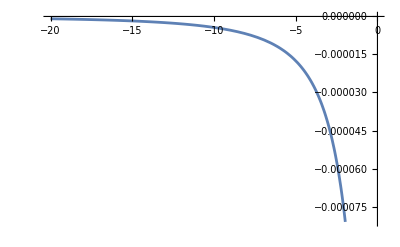

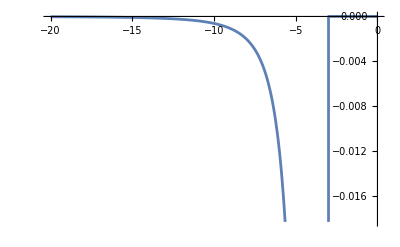

```mathematica
Plot[F[Ahexminus1,Ahexminus1,Ahexminus1]-F[Aroll1,Aroll2,Aroll3]/.μRoll[[2]],{K2,-20,0}]
Plot[F[Ahexminus1,Ahexminus1,Ahexminus1]-F[Aroll1,Aroll2,Aroll3]/.μRoll[[3]],{K2,-20,0}]
```

```mathematica
μHex=Solve[F[Ahexminus1,Ahexminus1,Ahexminus1]==F[Ahexplus1,Ahexplus1,Ahexplus1],μ0]//FullSimplify
```

{{μ0→1/(4 (-3+2 K2))}}

```mathematica
(*μMM=Solve[F[Ahexminus1,Ahexminus1,Ahexminus1]==F[Amm1,Amm2,Amm3],μ0]*)
```

```mathematica
Solve[Amm2==0,μ0]
```

{{μ0→3/(3+K2)^2}}

```mathematica
Series[F[Amm1,Amm2,Amm3]-F[Aroll1,0,0],{μ0,3/(3+K2)^2,2}]
```

((-3-K2) (μ0-3/(3+K2)^2)^2)/(12 (-3+K2))+O[μ0-3/(3+K2)^2]^3

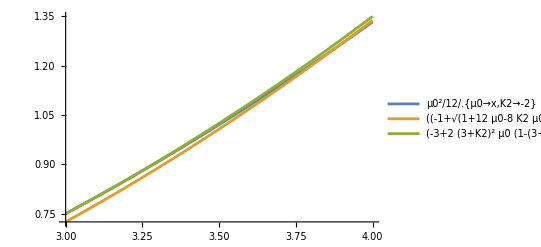

1/3

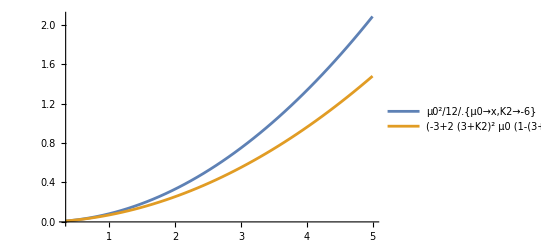

```mathematica
Plot[{Froll/.{μ0->x,K2->-2},Fhexminus/.{μ0->x,K2->-2},FMM/.{μ0->x,K2->-2}},{x,3,4},PlotLegends->"Expressions"]
μcrit=3/(3+K2)^2/.K2->-6
Plot[{Froll/.{μ0->x,K2->-6},FMM/.{μ0->x,K2->-6}},{x,μcrit,5},PlotLegends->"Expressions"]
```

```mathematica
D[FMM/.{μ0->x},x]//FullSimplify
D[Fhexminus/.{μ0->x},x]//FullSimplify
D[Froll/.{μ0->x},x]//FullSimplify
```

(1-2 (3+K2) x)/(2 (-9+K2^2))

-(3 (-1+(-6+4 K2) x+√(1+12 x-8 K2 x)))/(4 (3-2 K2)^2)

x/6

```mathematica
TeXForm[Limit[-(3 (-1+(-6+4 K2) x+√(1+12 x-8 K2 x)))/(4 (3-2 K2)^2)/x,{x->Infinity}]//FullSimplify]
```

\frac{3}{6-4 \text{K2}}

```mathematica
TeXForm[-(3 (-1+(-6+4 K2) x+√(1+12 x-8 K2 x)))/(4 (3-2 K2)^2)-3/(6-4 K2)*x//FullSimplify]
```

-\frac{3 \left(\sqrt{(12-8 \text{K2}) x+1}-1\right)}{4 (3-2 \text{K2})^2}

```mathematica
Solve[FullSimplify[D[FMM/.{μ0->x},x]-D[Fhexminus/.{μ0->x},x]]==0,x]
Solve[FullSimplify[D[FMM/.{μ0->x},x]-D[Froll/.{μ0->x},x]]==0,x]
Solve[FullSimplify[D[Fhexminus/.{μ0->x},x]-D[Froll/.{μ0->x},x]]==0,x]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{x→(6-K2)/(3+K2)^2}}

{{x→3/(3+K2)^2}}

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{x→0},{x→9/(4 (3+K2)^2)}}

```mathematica
FullSimplify[FullSimplify[D[FMM/.{μ0->x},x]-D[Fhexminus/.{μ0->x},x]]/.x->(6-K2)/(3+K2)^2,Assumptions->{-3+K2<0,3+K2<0}]
FullSimplify[FullSimplify[D[Froll/.{μ0->x},x]-D[Fhexminus/.{μ0->x},x]]/.x->9/(4 (3+K2)^2),Assumptions->{-3+K2<0,3+K2<0}]
```

(9 (-3+K2))/(2 (3-2 K2)^2 (3+K2))

(3 (-6+K2))/(2 (3-2 K2)^2 (3+K2))

Takeaway: F_MM’ > Fhexminus’ for all K2 < 0 and \mu0 > 0

```mathematica
(* check F_roll > F_hexminus when mixed modes bifurcate *)
FullSimplify[Froll>Fhexminus/.{μ0->3/(3+K2)^2},Assumptions->{K2<0}]
```

True

```mathematica
(* test asymptotic behaviour for μ0->Infinity *)
Limit[Fhexminus/μ0^2,μ0->Infinity]//FullSimplify
Limit[Froll/μ0^2,μ0->Infinity]
```

3/(12-8 K2)

1/12

# Calculations again with full parameter set

```mathematica
(* general vector field *)
Fgen[A1_,A2_,A3_]:=(μ0/2)*(A1^2+A2^2+A3^2)+β2*A1*A2*A3+(K0/4)*(A1^4+A2^4+A3^4)+(K2/2)*(A1^2*A2^2+A1^2*A3^2+A2^2*A3^2);
```

```mathematica
Aroll1=Sqrt[-μ0/K0];
Aroll2=0;
Aroll3=0;
```

```mathematica
Ahexplus1=(-β2-Sqrt[β2^2-4*μ0*(K0+2*K2)])/(2*(K0+2*K2));
```

```mathematica
Ahexminus1=(-β2+Sqrt[β2^2-4*μ0*(K0+2*K2)])/(2*(K0+2*K2));
Ahexminus2=(-β2+Sqrt[β2^2-4*μ0*K3])/(2*K3);
Ahexminus3=(-β2+Sqrt[β2^2-4*μ0*K3])/(2*K3);
```

```mathematica
Amm1=β2/(K0-K2);
Amm2=Sqrt[-(K0*β2^2+(K0-K2)^2*μ0)/((K0+K2)*(K0-K2)^2)];
Amm3=Sqrt[-(K0*β2^2+(K0-K2)^2*μ0)/((K0+K2)*(K0-K2)^2)];
```

```mathematica
Froll=Fgen[Aroll1,Aroll2,Aroll3]//FullSimplify
Fhexplus= Fgen[Ahexplus1,Ahexplus1,Ahexplus1]//FullSimplify
Fhexminus=FullSimplify[Fgen[Ahexminus1,Ahexminus1,Ahexminus1]]
FMM=Fgen[Amm1,Amm2,Amm2]//FullSimplify
```

-μ0^2/(4 K0)

-((β2+√(β2^2-4 (K0+2 K2) μ0))^2 (-6 (K0+2 K2) μ0+β2 (β2+√(β2^2-4 (K0+2 K2) μ0))))/(32 (K0+2 K2)^3)

((β2-√(β2^2-4 (K0+2 K2) μ0))^2 (6 (K0+2 K2) μ0+β2 (-β2+√(β2^2-4 (K0+2 K2) μ0))))/(32 (K0+2 K2)^3)

-(K0 β2^4+2 (K0-K2)^2 β2^2 μ0+2 (K0-K2)^3 μ0^2)/(4 (K0-K2)^3 (K0+K2))

```mathematica
FullSimplify[D[FMM/.{μ0->x},x]]
D[Fhexminus/.{μ0->x},x]//FullSimplify
D[Froll/.{μ0->x},x]//FullSimplify
D[FMM/.{μ0->x},x]//FullSimplify
```

-(2 K0 x-2 K2 x+β2^2)/(2 K0^2-2 K2^2)

-(3 (2 K0 x+4 K2 x+β2 (-β2+√(-4 (K0+2 K2) x+β2^2))))/(4 (K0+2 K2)^2)

-x/(2 K0)

-(2 K0 x-2 K2 x+β2^2)/(2 K0^2-2 K2^2)

```mathematica
D[FMM/.{μ0->x},x]/.{x->-K0*β2^2/(K0-K2)^2}//FullSimplify
D[Froll/.{μ0->x},x]/.{x->-K0*β2^2/(K0-K2)^2}//FullSimplify
FullSimplify[Expand[D[Fhexminus/.{μ0->x},x]/.{x->-K0*β2^2/(K0-K2)^2}],Assumptions->{K0+K2<0,5*K0+K2<0,β2>0}]
```

β2^2/(2 (K0-K2)^2)

β2^2/(2 (K0-K2)^2)

(3 β2^2 (3 K0^2+2 K0 K2+K2^2-√((K0+K2) (5 K0+K2)) Abs[K0-K2]))/(4 (K0-K2)^2 (K0+2 K2)^2)

```mathematica
-(2 (K0 - K2) x+β2^2)/(2 (K0-K2)*(K0+K2))//FullSimplify
```

-(2 K0 x-2 K2 x+β2^2)/(2 K0^2-2 K2^2)

```mathematica
Series[Fgen[Aroll1,Aroll2,Aroll3],{μ0,0,2}]//FullSimplify
FullSimplify[Series[Fgen[Ahexminus1,Ahexminus1,Ahexminus1],{μ0,0,3}],Assumptions->{β2>0}]
```

-μ0^2/(4 K0)+O[μ0]^3

μ0^3/(2 β2^2)+O[μ0]^4

```mathematica
TeXForm[Fhexplus-Fhexminus//FullSimplify]
```

-\frac{\text{$\beta $2} \left(\text{$\beta $2}^2-4 \text{$\mu $0} (\text{K0}+2 \text{K2})\right)^{3/2}}{4 (\text{K0}+2 \text{K2})^3}

```mathematica
μRoll=FullSimplify[Solve[Fhexminus==Froll,μ0],Assumptions->{β2>0,K0<0,K2<0,K2>K0}]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{μ0→0},{μ0→(K0 β2^2)/(2 K0^2+6 K0 K2+2 √2 √(K0 (K0+K2)^3))},{μ0→(K0 β2^2)/(-2 √2 √(K0 (K0+K2)^3)+2 K0 (K0+3 K2))}}

```mathematica
(* FullSimplify[Fgen[Ahexminus1,Ahexminus1,Ahexminus1]-Fgen[Aroll1,Aroll2,Aroll3]==0/.μRoll[[2]],Assumptions->{β2>0,K0<0,K2>K0,K2<0}] *)
FullSimplify[Fgen[Ahexminus1,Ahexminus1,Ahexminus1]-Fgen[Aroll1,Aroll2,Aroll3]==0/.μRoll[[3]],Assumptions->{β2>0,K0<0,K2>K0,K2<0}]
```

$Aborted

```mathematica
(* check if the potential root is larger than the bifurcation point of the mixed-modes in the appropriate parameter regime *)
(* μRoll[[2]] *)
FullSimplify[(K0 β2^2)/(2 K0^2+6 K0 K2+2 √2 √(K0 (K0+K2)^3))>=-K0*β2^2/(K0-K2)^2,Assumptions->{β2>0,K0<0,K2<0,K2>K0}]
(* μRoll[[3]] *)
FullSimplify[(K0 β2^2)/(-2 √2 √(K0 (K0+K2)^3)+2 K0 (K0+3 K2))>=-K0*β2^2/(K0-K2)^2,Assumptions->{β2>0,K0<0,K2<0,K2>K0}]
```

False

True

```mathematica
TeXForm[(K0 β2^2)/(-2 √2 √(K0 (K0+K2)^3)+2 K0 (K0+3 K2))]
```

\frac{\text{$\beta $2}^2 \text{K0}}{2 \text{K0} (\text{K0}+3 \text{K2})-2 \sqrt{2} \sqrt{\text{K0} (\text{K0}+\text{K2})^3}}